## Evolution of intermediate excitons in fluid argon and krypton P. Laporte et al, Phys. Rev. B 35, 6270-6280(1987)

In CGS units (4π e^2 ρ)/m, its unit is s^-2

For liquid argon at 78.4 K

```mathematica
(4 π(4.80320427 10^-10)^2)/(9.10938370 10^-28)24.8 10^21
```

7.89286×10^31

Switch it into eV

```mathematica
(4 π(4.80320427 10^-10)^2)/(9.10938370 10^-28)24.8 10^21(1.054571817 10^-34)^2/(1.60217662 10^-19)^2
```

34.1953

For liquid argon at 86.8 K

```mathematica
(4 π(4.80320427 10^-10)^2)/(9.10938370 10^-28)21.1 10^21(1.054571817 10^-34)^2/(1.60217662 10^-19)^2
```

29.0936

Change (4π e^2 ρ)/m from CGS units to SI units (e^2 ρ)/(ϵ_0 m) , its unit is s^-2

For liquid argon at 78.4 K

```mathematica
((1.60217662 10^-19)^2 24.8 10^27)/(8.8541878128×10^-12 9.10938370 10^-31)(1.054571817 10^-34)^2/(1.60217662 10^-19)^2
```

34.1953

For liquid argon at 86.8 K

```mathematica
((1.60217662 10^-19)^2 21.1 10^27)/(8.8541878128×10^-12 9.10938370 10^-31)(1.054571817 10^-34)^2/(1.60217662 10^-19)^2
```

29.0936

The results from CGS units and SI units are consistent!

The complex dielectric constant for liquid argon at 86.8 K as a function of the input monochromatic light with unit of eV

```mathematica
epsilon[x_]:=2.0+((1.60217662 10^-19)^2 21.1 10^27)/(8.8541878128×10^-12 9.10938370 10^-31)(1.054571817 10^-34)^2/(1.60217662 10^-19)^2(0.28/(11.95^2-x^2-ⅈ x 0.15)+0.398/(11.730^2-x^2-ⅈ x 0.14))
```

The real part of the complex dielectric constant.

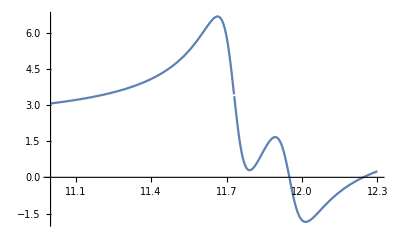

```mathematica
Plot[Re[epsilon[x]],{x,11.0 ,12.3},AxesOrigin->{11.0,0.0}]
```

The imaginary part of the complex dielectric constant.

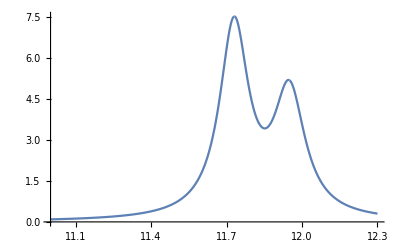

```mathematica
Plot[Im[epsilon[x]],{x,11.0 ,12.3},AxesOrigin->{11.0,0.0}]
```

The real refractive index for light in unit of eV

```mathematica
n[x_]:=√((Re[epsilon[x]]+√(Re[epsilon[x]]^2+Im[epsilon[x]]^2))/2)
```

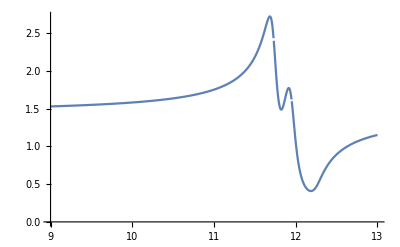

```mathematica
Plot[n[x],{x,9.0,13.0},AxesOrigin->{9.0,0.0}]
```

The imaginary refractive index  for light in unit of eV

```mathematica
k[x_]:=√((-Re[epsilon[x]]+√(Re[epsilon[x]]^2+Im[epsilon[x]]^2))/2)
```

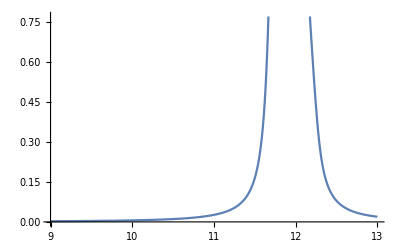

```mathematica
Plot[k[x],{x,9.0,13.0},AxesOrigin->{9.0,0.0}]
```

The optical absorption coefficient α=(2ω k)/c for light in unit of eV

```mathematica
alpha[x_]:=(2k[x](x 1.60217662 10^-19)/(1.054571817 10^-34))/299792458
```

```mathematica
alpha[1]
```

511.245

```mathematica
(1.60217662 10^-19)/(1.054571817 10^-34)
```

1.51927×10^15

nm to eV convertor

```mathematica
nmTOeV[x_]:=(6.62607015 10^-34 299792458)/(x 10^-9 1.60217662 10^-19)
```

```mathematica
nmTOeV[128]
```

9.68627

```mathematica
nmTOeV[104.8]
```

11.8306

```mathematica
nmTOeV[106.6]
```

11.6308

```mathematica
nmTOeV[104.82]
```

11.8283

```mathematica
nmTOeV[106.66]
```

11.6242

The real refractive index in unit of nm

```mathematica
n[nmTOeV[128]]
```

1.559

eV to nm convertor

```mathematica
eVTOnm[x_]:=((6.62607015 10^-34 299792458)/(x 10^-9 1.60217662 10^-19))^1
```

```mathematica
eVTOnm[11.79]
```

105.16

```mathematica
eVTOnm[12.05]
```

102.891

```mathematica
eVTOnm[11.73]
```

105.698

```mathematica
eVTOnm[11.95]
```

103.752

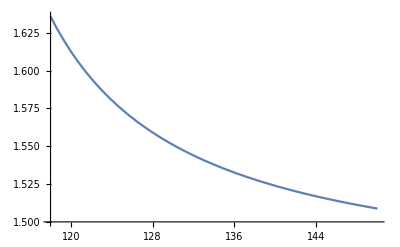

```mathematica
Plot[n[nmTOeV[x]],{x,118,150},AxesOrigin->{118,1.5}]
```

The imaginary refractive index in unit of nm

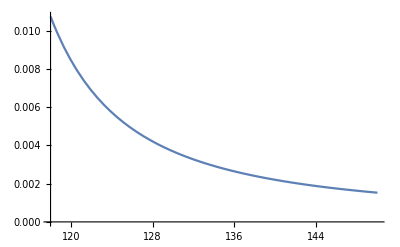

```mathematica
Plot[k[nmTOeV[x]],{x,118,150},AxesOrigin->{118,0}]
```

The optical absorption coefficient α=(2ω k)/c for light in unit of nm

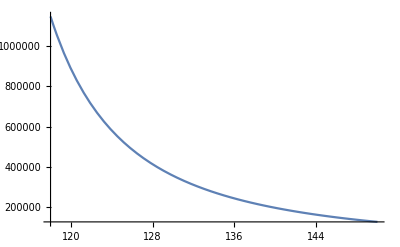

```mathematica
Plot[alpha[nmTOeV[x]],{x,118,150}]
```

```mathematica
k[9.68627]
```

0.00418325

n0 related to 11.95 eV i.e. 103.752 near gas peak 104.82

```mathematica
alphaLiquidArgonumMiss104[x_]:=1.2055 10^-2 2/3 21.1 10^27/((6.02214 10^23)/(22.413969545014 10^-3))(0.0415/(87.892-x^-2)+4.3330/(214.02-x^-2))
```

```mathematica
alphaLiquidArgonnmMiss104[x_]:=alphaLiquidArgonumMiss104[nmTOum[x]]
```

```mathematica
nLiquidArgonMiss104[x_]:=√((2 alphaLiquidArgonnmMiss104[x]+1)/(1-alphaLiquidArgonnmMiss104[x]))
```

```mathematica
nLiquidArgonMiss104[104.82]
```

1.21741

```mathematica
nLiquidArgonMiss104[103.75246821471815]
```

1.27654

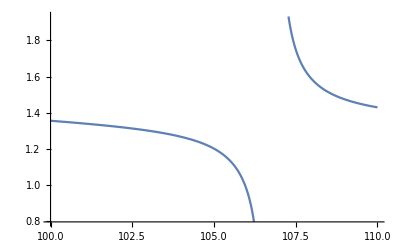

```mathematica
Plot[nLiquidArgonMiss104[x],{x,100,110}]
```

n0 related to 11.73 eV i.e. 105.698 nm near gas peak 106.66

```mathematica
alphaLiquidArgonumMiss106[x_]:=1.2055 10^-2 2/3 21.1 10^27/((6.02214 10^23)/(22.413969545014 10^-3))(0.2075/(91.012-x^-2)+4.3330/(214.02-x^-2))
```

```mathematica
alphaLiquidArgonnmMiss106[x_]:=alphaLiquidArgonumMiss106[nmTOum[x]]
```

```mathematica
nLiquidArgonMiss106[x_]:=√((2 alphaLiquidArgonnmMiss106[x]+1)/(1-alphaLiquidArgonnmMiss106[x]))
```

```mathematica
nLiquidArgonMiss106[106.66]
```

2.50692

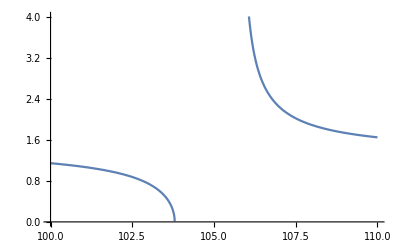

```mathematica
Plot[nLiquidArgonMiss106[x],{x,100,110}]
```